Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0.740741^ComplexInfinity encountered.

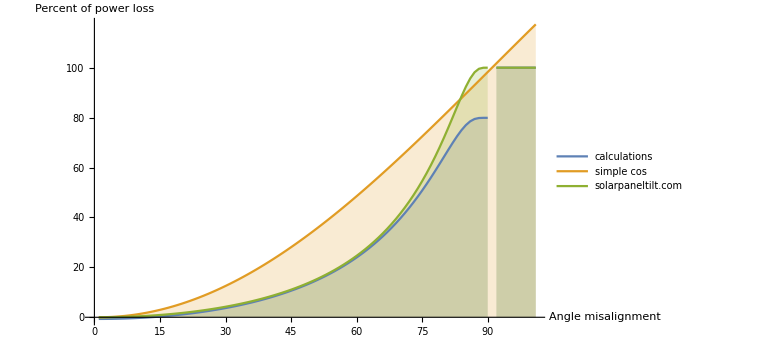

```mathematica
directPower[x_?NumericQ]  := ( (* param: index, solar panel angle in degrees, date. returns W/m^2 *)
theta=x; (* solar zenith (misalignment) in radians *)
(* here comes the magik formula from http://www.powerfromthesun.net/Book/chapter02/chapter02.html#ZEqnNum929295 for a clear day *)
n= QuantityMagnitude[Quantity[d - DateObject[{2016,1,1}]]]; (* day of year *)
i= 1367 (1+0.034 Cos[360*n/365.25]);
aZero = 0.4237 - 0.00821 36;
aOne = 0.5055 + 0.00595 6.5^2;
k = 0.2711 + 0.01858 2.5^2;
If[Cos[theta]<0,
0,
i (aZero + aOne E^(-k/Cos[theta])) (* If the sun is more than 90 degrees off, the formula is not correct, and we set the value to be 0 *)
] 
)

directPowerPercent := Function[
(1-directPower[#1]/860)*100
]

solarPanelTilt[z_] := (
If[z>90,
100,
i =1.35*(1/1.35)^(Sec[z*Pi/180]);
(1-i)*100
]
)

(* DiscretePlot[1-Cos[x*Pi/180],{x,0,90,2},ImageSize->Large] *)

(*Show[DiscretePlot[directPowerPercent[x*Pi/180],{x,0,90,2},ImageSize->Large],
DiscretePlot[100*(1-Cos[x*Pi/180]),{x,0,90,2},ImageSize->Large],DiscretePlot[solarPanelTilt[x],{x,0,90,2},ImageSize->Large]
]*)

ListLinePlot[{Table[directPowerPercent[x*Pi/180],{x,0,100}],
Table[100*(1-Cos[x*Pi/180]),{x,0,100}],
Table[solarPanelTilt[x],{x,0,100}]},Filling -> Axis,PlotLegends -> {calculations,simple cos,solarpaneltilt.com},ImageSize -> Large,AxesLabel-> {"Angle misalignment","Percent of power loss"}]
```